## Мухамадиев Владимир

# Задание 11

## Загрузка и предварительная обработка

```mathematica
(*Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"]*)
```

```mathematica
Needs["IGraphM`"]
```

IGraph/M 0.4 (April 2, 2020)
Evaluate IGDocumentation[] to get started.

```mathematica
datatest=Import[NotebookDirectory[]<>"\\k-core-exp.txt","Data"];
```

```mathematica
eltest=Table[datatest⟦i,1⟧<->datatest⟦i,2⟧,{i,1,Length[datatest]}];
```

```mathematica
gtest=Graph[eltest];
```

```mathematica
airports=Import[NotebookDirectory[]<>"\\airports.graphml"];
```

```mathematica
data1=Import[NotebookDirectory[]<>"\\asoiaf-book1-edges.csv","CSV"];
```

```mathematica
el1=Table[data1⟦i,1⟧<->data1⟦i,2⟧,{i,2,Length[data1]}];
```

```mathematica
ew1=data1⟦2;;All,4⟧;
```

```mathematica
g1=Graph[el1,EdgeWeight->ew1];
```

```mathematica
data2=Import[NotebookDirectory[]<>"\\asoiaf-book2-edges.csv","CSV"];
```

```mathematica
el2=Table[data2⟦i,1⟧<->data2⟦i,2⟧,{i,2,Length[data2]}];
```

```mathematica
ew2=data2⟦2;;All,4⟧;
```

```mathematica
g2=Graph[el2,EdgeWeight->ew2];
```

```mathematica
data3=Import[NotebookDirectory[]<>"\\asoiaf-book3-edges.csv","CSV"];
```

```mathematica
el3=Table[data3⟦i,1⟧<->data3⟦i,2⟧,{i,2,Length[data3]}];
```

```mathematica
ew3=data3⟦2;;All,4⟧;
```

```mathematica
g3=Graph[el3,EdgeWeight->ew3];
```

```mathematica
data4=Import[NotebookDirectory[]<>"\\asoiaf-book4-edges.csv","CSV"];
```

```mathematica
el4=Table[data4⟦i,1⟧<->data4⟦i,2⟧,{i,2,Length[data4]}];
```

```mathematica
ew4=data4⟦2;;All,4⟧;
```

```mathematica
g4=Graph[el4,EdgeWeight->ew4];
```

```mathematica
data5=Import[NotebookDirectory[]<>"\\asoiaf-book5-edges.csv","CSV"];
```

```mathematica
el5=Table[data5⟦i,1⟧<->data5⟦i,2⟧,{i,2,Length[data5]}];
```

```mathematica
ew5=data5⟦2;;All,4⟧;
```

```mathematica
g5=Graph[el5,EdgeWeight->ew5];
```

## 1. Разложение по k-core и визуализация сложной сети

### Функция которая приводит список ребер к виду, где в каждом ребре v_1<->v_2,v_1≤v_2

```mathematica
EdgeSort[edgelist_]:=Module[{out=edgelist},Do[If[edgelist⟦i,1⟧>edgelist⟦i,2⟧,out⟦i⟧=edgelist⟦i,2⟧<->edgelist⟦i,1⟧],{i,1,Length[edgelist]}];out]
```

### Рандомизация графа которая не создает новых петель и мультиребер

```mathematica
GraphRandomization[g_,n_]:=Module[{el=EdgeSort[EdgeList[g]],eltemp={},vltemp={},temp={{},{}},k=0},Do[temp⟦1⟧=RandomChoice[el](*Выбираем первое ребро/петлю*);eltemp=DeleteCases[el,temp⟦1⟧](*Создаем временную выборку из ребер/петель и удалаем из нее все мультиребра/мультипетли для выбранного ребра/петли*);If[temp⟦1,1⟧==temp⟦1,2⟧,(*Алгоритм выбрал петлю*)eltemp=DeleteCases[eltemp,v_<->v_](*удаляем из временной выбрки все петли*);vltemp=Flatten[{Cases[eltemp,temp⟦1,1⟧<->_],Cases[eltemp,_<->temp⟦1,1⟧]}];vltemp=DeleteDuplicates[Flatten[{vltemp⟦All,1⟧,vltemp⟦All,2⟧}]](*Список вершин с которыми граничит выбранная петля*);Do[eltemp=DeleteCases[eltemp,vltemp⟦j⟧<->_];eltemp=DeleteCases[eltemp,_<->vltemp⟦j⟧],{j,1,Length[vltemp]}](*Удаляем из временной выборки все ребра/петли, вершины которых связаны с данной петлей*);If[eltemp=={},i++;Goto[end](*Алгоритм выбрал петлю которую нельзя изменить, так как до любой вершины из нее можно добраться в два шага. Переходим в конец цикла и считаем что на этом шаге ничего не поменялось*),temp⟦2⟧=RandomChoice[eltemp](*Выбираем второе ребро*)],(*Алгоритм выбрал ребро*)vltemp=Flatten[{Cases[eltemp,temp⟦1,1⟧<->_],Cases[eltemp,_<->temp⟦1,1⟧],Cases[eltemp,temp⟦1,2⟧<->_],Cases[eltemp,_<->temp⟦1,2⟧]}];vltemp=DeleteDuplicates[Flatten[{vltemp⟦All,1⟧,vltemp⟦All,2⟧}]](*Список вершин с которыми граничит выбранное ребро*);Do[eltemp=DeleteCases[eltemp,vltemp⟦j⟧<->_];eltemp=DeleteCases[eltemp,_<->vltemp⟦j⟧],{j,1,Length[vltemp]}](*Удаляем из временной выборки все ребра/петли, вершины которых связаны с данным ребром*);If[eltemp=={},i++;Goto[end](*Алгоритм выбрал ребро которое нельзя изменить, так как до любой вершины из него можно добраться в два шага. Переходим в конец цикла и считаем что на этом шаге ничего не поменялось*),temp⟦2⟧=RandomChoice[eltemp](*Выбираем второе ребро/петлю*)]];k=1;While[(el⟦k⟧===temp⟦1⟧)==False,k++];el=Delete[el,k];k=1;While[(el⟦k⟧===temp⟦2⟧)==False,k++];el=Delete[el,k](*Удаляем из списка ребер выбранные*);If[RandomInteger[{1,2}]==1(*Случайно выбираем как переключить ребра и добавляем новые к списку ребер*),AppendTo[el,EdgeSort[{temp⟦1,1⟧<->temp⟦2,1⟧}]⟦1⟧];AppendTo[el,EdgeSort[{temp⟦1,2⟧<->temp⟦2,2⟧}]⟦1⟧],AppendTo[el,EdgeSort[{temp⟦1,1⟧<->temp⟦2,2⟧}]⟦1⟧];AppendTo[el,EdgeSort[{temp⟦1,2⟧<->temp⟦2,1⟧}]⟦1⟧]];Label[end],{i,1,n}];Graph[el]]
```

### k-core распределение

```mathematica
KCoreDistribution[graph_]:=Table[Length[Flatten[KCoreComponents[graph,i]]]/VertexCount[graph],{i,1,Max[VertexDegree[graph]]}]
```

```mathematica
GraphRandomizationKCoreDistributionEvolution[graph_,steps_]:=Module[{temp=graph,out=ConstantArray[{},steps+1]},out⟦1⟧=KCoreDistribution[temp];Do[temp=GraphRandomization[temp,1];out⟦l⟧=KCoreDistribution[temp],{l,2,steps+1}];out=outᵀ;Table[{Range[steps+1],out⟦i⟧}ᵀ,{i,1,Max[VertexDegree[graph]]}];{temp,out}]
```

#### На малом графе

```mathematica
dg=GraphRandomizationKCoreDistributionEvolution[gtest,1000];
```

```mathematica
ListLinePlot[dg⟦2,1;;3⟧,ImageSize->Large,PlotLabels->Table[ToString[i]<>"-core",{i,1,3}],AxesLabel->{None,"%"},PlotRange->All]
```

-Graphics-

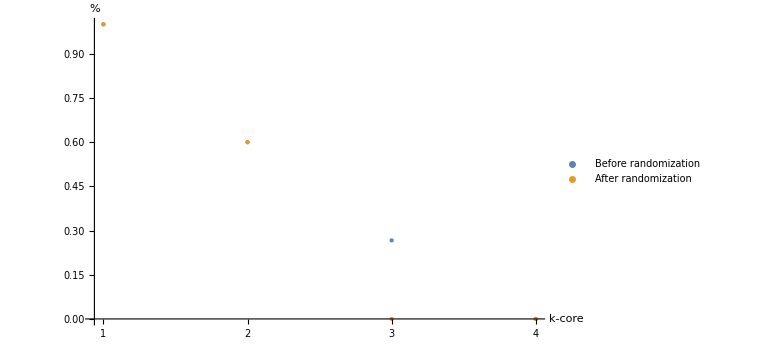

```mathematica
ListPlot[{{Range[4],KCoreDistribution[gtest]⟦1;;4⟧}ᵀ,{Range[4],KCoreDistribution[dg⟦1⟧]⟦1;;4⟧}ᵀ},PlotRange->All,PlotStyle->PointSize[Large],Ticks->{Range[4],Automatic},PlotLegends->Placed[{"Before randomization","After randomization"},Below],AxesLabel->{"k-core","%"},ImageSize->Large]
```

#### На большом графе

```mathematica
da=Import[NotebookDirectory[]<>"da.m"];(*da=GraphRandomizationKCoreDistributionEvolution[airports,1000];*)
```

```mathematica
ListLinePlot[da⟦2,1;;31⟧,ImageSize->Large,PlotLabels->Table[ToString[i]<>"-core",{i,1,31}],PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[da⟦2,20;;31⟧,ImageSize->Large,PlotLabels->Table[ToString[i]<>"-core",{i,20,31}],PlotRange->All]
```

-Graphics-

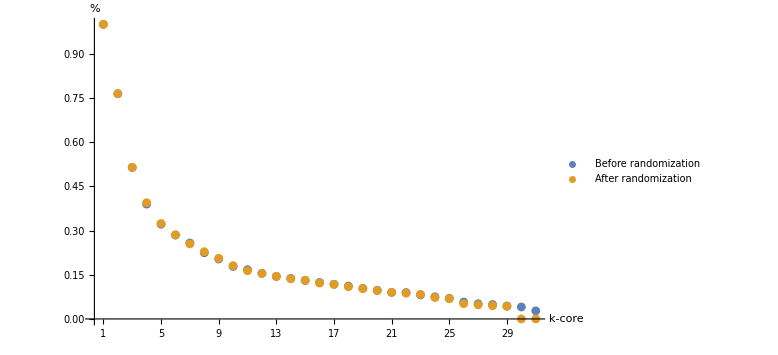

```mathematica
ListPlot[{{Range[31],KCoreDistribution[airports]⟦1;;31⟧}ᵀ,{Range[31],KCoreDistribution[da⟦1⟧]⟦1;;31⟧}ᵀ},PlotRange->All,Ticks->{Range[31],Automatic},PlotLegends->Placed[{"Before randomization","After randomization"},Below],AxesLabel->{"k-core","%"},ImageSize->Large]
```

### Укладка графа по k-shell

```mathematica
CircleLayout[n_]:=Table[{Cos[(2π i)/n],Sin[(2π i)/n]},{i,n}]
```

```mathematica
Degeneracy[g_]:=Module[{i=1},While[KCoreComponents[g,i]≠{},++i];i-1]
```

```mathematica
KShellComponents[graph_]:=Table[Complement[Flatten[KCoreComponents[graph,i]],Flatten[KCoreComponents[graph,i+1]]],{i,1,Degeneracy[graph]}]
```

```mathematica
KShellRadialEmbedding[graph_,imagesize_]:=Module[{ksc=KShellComponents[graph]},HighlightGraph[Graph[graph,VertexCoordinates->Flatten[Table[Map[{#⟦1⟧->#⟦2⟧}&,{ksc⟦i⟧,(Length[ksc]+1-i) CircleLayout[Length[ksc⟦i⟧]]}ᵀ],{i,1,Length[ksc]}]]],Table[Style[ksc⟦i⟧,ColorData["TemperatureMap"][i/Length[ksc]]],{i,Length[ksc]}],VertexSize->Medium,ImageSize->imagesize]]
```

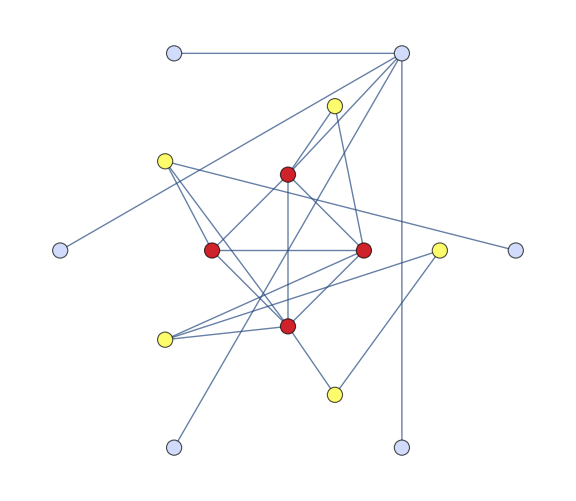

```mathematica
KShellRadialEmbedding[gtest,Large]
```

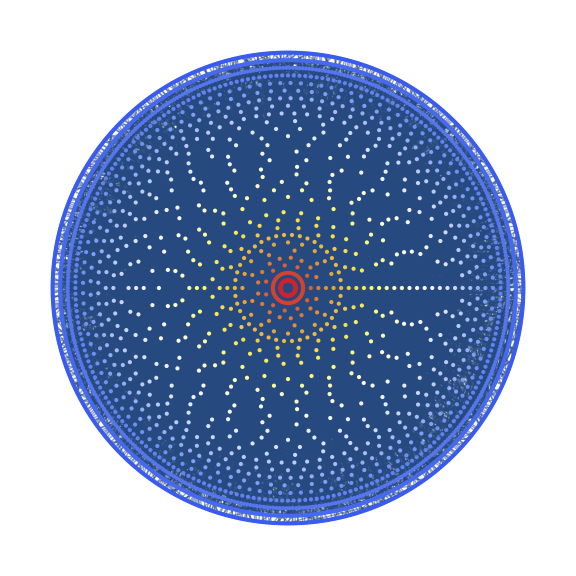

```mathematica
KShellRadialEmbedding[airports,Large]
```

## 2. Предсказание связей в сложных сетях

```mathematica
TopLinksPreditions[graph_,metrics_]:=Module[{vnm={VertexList[graph]}ᵀ.{VertexList[graph]},nl=DeleteCases[Map[If[#⟦1⟧≥#⟦2⟧,{},#]&,Position[Normal[AdjacencyMatrix[graph]],0]],{}],sim=metrics[graph]},ReverseSortBy[Table[{vnm⟦nl⟦i,1⟧,nl⟦i,2⟧⟧⟦1⟧<->vnm⟦nl⟦i,1⟧,nl⟦i,2⟧⟧⟦2⟧,sim⟦nl⟦i,1⟧,nl⟦i,2⟧⟧},{i,1,Length[nl]}],Last]]
```

### Число общих соседей

```mathematica
(c1=TopLinksPreditions[g1,IGCocitationCoupling]⟦1;;10⟧)//MatrixForm
```

(Arya-Stark<->Tyrion-Lannister | 16
Cersei-Lannister<->Robb-Stark | 14
Bran-Stark<->Jaime-Lannister | 14
Sansa-Stark<->Tywin-Lannister | 13
Petyr-Baelish<->Robb-Stark | 13
Joffrey-Baratheon<->Jory-Cassel | 13
Rodrik-Cassel<->Sansa-Stark | 12
Robert-Baratheon<->Rodrik-Cassel | 12
Jon-Snow<->Petyr-Baelish | 12
Jon-Arryn<->Sansa-Stark | 12)

### Коэффициент Салтона

```mathematica
(c2=TopLinksPreditions[g1,N[VertexCosineSimilarity[#]]&]⟦1;;10⟧)//MatrixForm
```

(Varly<->Wylla | 1.
Tregar<->Wylla | 1.
Tregar<->Varly | 1.
Tobho-Mott<->Wylla | 1.
Tobho-Mott<->Varly | 1.
Tobho-Mott<->Tregar | 1.
Porther<->Wylla | 1.
Porther<->Varly | 1.
Porther<->Tregar | 1.
Porther<->Tobho-Mott | 1.)

### Коэффициент Жаккара

```mathematica
(c3=TopLinksPreditions[g1,IGJaccardSimilarity]⟦1;;10⟧)//MatrixForm
```

(Varly<->Wylla | 1.
Tregar<->Wylla | 1.
Tregar<->Varly | 1.
Tobho-Mott<->Wylla | 1.
Tobho-Mott<->Varly | 1.
Tobho-Mott<->Tregar | 1.
Porther<->Wylla | 1.
Porther<->Varly | 1.
Porther<->Tregar | 1.
Porther<->Tobho-Mott | 1.)

### Коэффициент Серенсена

```mathematica
(c4=TopLinksPreditions[g1,IGDiceSimilarity]⟦1;;10⟧)//MatrixForm
```

(Varly<->Wylla | 1.
Tregar<->Wylla | 1.
Tregar<->Varly | 1.
Tobho-Mott<->Wylla | 1.
Tobho-Mott<->Varly | 1.
Tobho-Mott<->Tregar | 1.
Porther<->Wylla | 1.
Porther<->Varly | 1.
Porther<->Tregar | 1.
Porther<->Tobho-Mott | 1.)

### Коэффициент предпочтительного присоединения

```mathematica
(c5=TopLinksPreditions[g1,{VertexDegree[#]}ᵀ.{VertexDegree[#]}&]⟦1;;10⟧)//MatrixForm
```

(Drogo<->Eddard-Stark | 1254
Arya-Stark<->Tyrion-Lannister | 1242
Jaime-Lannister<->Jon-Snow | 1073
Cersei-Lannister<->Robb-Stark | 1050
Jory-Cassel<->Tyrion-Lannister | 966
Daenerys-Targaryen<->Tyrion-Lannister | 966
Jon-Snow<->Petyr-Baelish | 962
Bran-Stark<->Jaime-Lannister | 928
Benjen-Stark<->Eddard-Stark | 924
Petyr-Baelish<->Robb-Stark | 910)

### Коэффициент Адамика-Адара

```mathematica
(c6=TopLinksPreditions[g1,IGInverseLogWeightedSimilarity]⟦1;;10⟧)//MatrixForm
```

(Arya-Stark<->Tyrion-Lannister | 5.31863
Bran-Stark<->Jaime-Lannister | 4.30283
Sansa-Stark<->Tywin-Lannister | 4.23827
Cersei-Lannister<->Robb-Stark | 4.13939
Joffrey-Baratheon<->Jory-Cassel | 3.98908
Petyr-Baelish<->Robb-Stark | 3.92302
Jaime-Lannister<->Pycelle | 3.8436
Jon-Arryn<->Sansa-Stark | 3.72105
Joffrey-Baratheon<->Jon-Arryn | 3.72105
Jon-Snow<->Petyr-Baelish | 3.57408)

### Общее по числу общих соседей, коэффициенту предпочтительного присоединения и коэффициенту Адамика-Адара

```mathematica
ci=c1⟦All,1⟧∪c5⟦All,1⟧∪c6⟦All,1⟧
```

{Arya-Stark<->Tyrion-Lannister,Benjen-Stark<->Eddard-Stark,Bran-Stark<->Jaime-Lannister,Cersei-Lannister<->Robb-Stark,Daenerys-Targaryen<->Tyrion-Lannister,Drogo<->Eddard-Stark,Jaime-Lannister<->Jon-Snow,Jaime-Lannister<->Pycelle,Joffrey-Baratheon<->Jon-Arryn,Joffrey-Baratheon<->Jory-Cassel,Jon-Arryn<->Sansa-Stark,Jon-Snow<->Petyr-Baelish,Jory-Cassel<->Tyrion-Lannister,Petyr-Baelish<->Robb-Stark,Robert-Baratheon<->Rodrik-Cassel,Rodrik-Cassel<->Sansa-Stark,Sansa-Stark<->Tywin-Lannister}

#### 2 книга

```mathematica
{ci,Table[ContainsAll[EdgeList[g2],{ci⟦i⟧}]||ContainsAll[EdgeList[g2],{Reverse[ci⟦i⟧]}],{i,1,Length[ci]}]}ᵀ//MatrixForm
```

(Arya-Stark<->Tyrion-Lannister | True
Benjen-Stark<->Eddard-Stark | False
Bran-Stark<->Jaime-Lannister | False
Cersei-Lannister<->Robb-Stark | True
Daenerys-Targaryen<->Tyrion-Lannister | False
Drogo<->Eddard-Stark | False
Jaime-Lannister<->Jon-Snow | True
Jaime-Lannister<->Pycelle | False
Joffrey-Baratheon<->Jon-Arryn | False
Joffrey-Baratheon<->Jory-Cassel | False
Jon-Arryn<->Sansa-Stark | False
Jon-Snow<->Petyr-Baelish | False
Jory-Cassel<->Tyrion-Lannister | False
Petyr-Baelish<->Robb-Stark | False
Robert-Baratheon<->Rodrik-Cassel | False
Rodrik-Cassel<->Sansa-Stark | False
Sansa-Stark<->Tywin-Lannister | False)

#### 3 книга

```mathematica
{ci,Table[ContainsAll[EdgeList[g3],{ci⟦i⟧}]||ContainsAll[EdgeList[g3],{Reverse[ci⟦i⟧]}],{i,1,Length[ci]}]}ᵀ//MatrixForm
```

(Arya-Stark<->Tyrion-Lannister | True
Benjen-Stark<->Eddard-Stark | False
Bran-Stark<->Jaime-Lannister | False
Cersei-Lannister<->Robb-Stark | False
Daenerys-Targaryen<->Tyrion-Lannister | False
Drogo<->Eddard-Stark | False
Jaime-Lannister<->Jon-Snow | False
Jaime-Lannister<->Pycelle | False
Joffrey-Baratheon<->Jon-Arryn | False
Joffrey-Baratheon<->Jory-Cassel | False
Jon-Arryn<->Sansa-Stark | False
Jon-Snow<->Petyr-Baelish | False
Jory-Cassel<->Tyrion-Lannister | False
Petyr-Baelish<->Robb-Stark | True
Robert-Baratheon<->Rodrik-Cassel | False
Rodrik-Cassel<->Sansa-Stark | False
Sansa-Stark<->Tywin-Lannister | True)

#### 4 книга

```mathematica
{ci,Table[ContainsAll[EdgeList[g4],{ci⟦i⟧}]||ContainsAll[EdgeList[g4],{Reverse[ci⟦i⟧]}],{i,1,Length[ci]}]}ᵀ//MatrixForm
```

(Arya-Stark<->Tyrion-Lannister | False
Benjen-Stark<->Eddard-Stark | False
Bran-Stark<->Jaime-Lannister | False
Cersei-Lannister<->Robb-Stark | False
Daenerys-Targaryen<->Tyrion-Lannister | False
Drogo<->Eddard-Stark | False
Jaime-Lannister<->Jon-Snow | False
Jaime-Lannister<->Pycelle | True
Joffrey-Baratheon<->Jon-Arryn | False
Joffrey-Baratheon<->Jory-Cassel | False
Jon-Arryn<->Sansa-Stark | False
Jon-Snow<->Petyr-Baelish | False
Jory-Cassel<->Tyrion-Lannister | False
Petyr-Baelish<->Robb-Stark | False
Robert-Baratheon<->Rodrik-Cassel | False
Rodrik-Cassel<->Sansa-Stark | False
Sansa-Stark<->Tywin-Lannister | True)

#### 5 книга

```mathematica
{ci,Table[ContainsAll[EdgeList[g5],{ci⟦i⟧}]||ContainsAll[EdgeList[g5],{Reverse[ci⟦i⟧]}],{i,1,Length[ci]}]}ᵀ//MatrixForm
```

(Arya-Stark<->Tyrion-Lannister | False
Benjen-Stark<->Eddard-Stark | False
Bran-Stark<->Jaime-Lannister | False
Cersei-Lannister<->Robb-Stark | False
Daenerys-Targaryen<->Tyrion-Lannister | True
Drogo<->Eddard-Stark | False
Jaime-Lannister<->Jon-Snow | False
Jaime-Lannister<->Pycelle | False
Joffrey-Baratheon<->Jon-Arryn | False
Joffrey-Baratheon<->Jory-Cassel | False
Jon-Arryn<->Sansa-Stark | False
Jon-Snow<->Petyr-Baelish | False
Jory-Cassel<->Tyrion-Lannister | False
Petyr-Baelish<->Robb-Stark | False
Robert-Baratheon<->Rodrik-Cassel | False
Rodrik-Cassel<->Sansa-Stark | False
Sansa-Stark<->Tywin-Lannister | False)

```mathematica
Module[{vnm={VertexList[g1]}ᵀ.{VertexList[g1]},nl=DeleteCases[Map[If[#⟦1⟧≥#⟦2⟧,{},#]&,Position[Normal[AdjacencyMatrix[g1]],0]],{}],sim=Module[{vw=Table[Total[{Cases[{el1,ew1}ᵀ,{VertexList[g1]⟦i⟧<->_,_}]⟦All,2⟧,Cases[{el1,ew1}ᵀ,{_<->VertexList[g1]⟦i⟧,_}]⟦All,2⟧},2],{i,1,VertexCount[g1]}]},{vw}ᵀ.{vw}*{VertexDegree[g1]}ᵀ.{VertexDegree[g1]}]},ReverseSortBy[Table[{vnm⟦nl⟦i,1⟧,nl⟦i,2⟧⟧⟦1⟧<->vnm⟦nl⟦i,1⟧,nl⟦i,2⟧⟧⟦2⟧,sim⟦nl⟦i,1⟧,nl⟦i,2⟧⟧},{i,1,Length[nl]}],Last]]⟦1;;10⟧//MatrixForm
```

(Drogo<->Eddard-Stark | 412194816
Arya-Stark<->Tyrion-Lannister | 347139000
Daenerys-Targaryen<->Tyrion-Lannister | 278159700
Daenerys-Targaryen<->Jon-Snow | 269861424
Jon-Snow<->Petyr-Baelish | 236067104
Cersei-Lannister<->Robb-Stark | 229723200
Catelyn-Stark<->Daenerys-Targaryen | 208015080
Jaime-Lannister<->Jon-Snow | 202736912
Eddard-Stark<->Jeor-Mormont | 199402632
Luwin<->Robert-Baratheon | 177849000)

### Взвешенное предпочтительное присоединение S_xy=k(x)w(x)k(y)w(y), вес вершины - сумма весов ребер

```mathematica
(cs=Module[{vnm={VertexList[g1]}ᵀ.{VertexList[g1]},nl=DeleteCases[Map[If[#⟦1⟧≥#⟦2⟧,{},#]&,Position[Normal[AdjacencyMatrix[g1]],0]],{}],sim=Module[{vw=Table[Total[{Cases[{el1,ew1}ᵀ,{VertexList[g1]⟦i⟧<->_,_}]⟦All,2⟧,Cases[{el1,ew1}ᵀ,{_<->VertexList[g1]⟦i⟧,_}]⟦All,2⟧},2],{i,1,VertexCount[g1]}]},{vw}ᵀ.{vw}*{VertexDegree[g1]}ᵀ.{VertexDegree[g1]}]},ReverseSortBy[Table[{vnm⟦nl⟦i,1⟧,nl⟦i,2⟧⟧⟦1⟧<->vnm⟦nl⟦i,1⟧,nl⟦i,2⟧⟧⟦2⟧,sim⟦nl⟦i,1⟧,nl⟦i,2⟧⟧},{i,1,Length[nl]}],Last]]⟦1;;10⟧)//MatrixForm
```

(Drogo<->Eddard-Stark | 412194816
Arya-Stark<->Tyrion-Lannister | 347139000
Daenerys-Targaryen<->Tyrion-Lannister | 278159700
Daenerys-Targaryen<->Jon-Snow | 269861424
Jon-Snow<->Petyr-Baelish | 236067104
Cersei-Lannister<->Robb-Stark | 229723200
Catelyn-Stark<->Daenerys-Targaryen | 208015080
Jaime-Lannister<->Jon-Snow | 202736912
Eddard-Stark<->Jeor-Mormont | 199402632
Luwin<->Robert-Baratheon | 177849000)

#### Сравнение

```mathematica
Grid[{Prepend[Range[10],"№"],Prepend[c5ᵀ⟦1⟧,"Без весов"],Prepend[csᵀ⟦1⟧,"С весами"]}ᵀ,Background->{None,{{{Pink,Lighter[Blue,0.7]}},{1->Gray}}},Dividers->All,Spacings->{1, 1}]
```

№ | Без весов | С весами
1 | Drogo<->Eddard-Stark | Drogo<->Eddard-Stark
2 | Arya-Stark<->Tyrion-Lannister | Arya-Stark<->Tyrion-Lannister
3 | Jaime-Lannister<->Jon-Snow | Daenerys-Targaryen<->Tyrion-Lannister
4 | Cersei-Lannister<->Robb-Stark | Daenerys-Targaryen<->Jon-Snow
5 | Jory-Cassel<->Tyrion-Lannister | Jon-Snow<->Petyr-Baelish
6 | Daenerys-Targaryen<->Tyrion-Lannister | Cersei-Lannister<->Robb-Stark
7 | Jon-Snow<->Petyr-Baelish | Catelyn-Stark<->Daenerys-Targaryen
8 | Bran-Stark<->Jaime-Lannister | Jaime-Lannister<->Jon-Snow
9 | Benjen-Stark<->Eddard-Stark | Eddard-Stark<->Jeor-Mormont
10 | Petyr-Baelish<->Robb-Stark | Luwin<->Robert-Baratheon